```mathematica
Subscript[τ, r]=Subscript[τ, m]=τ
```

```mathematica
Subscript[c, r]=y
```

```mathematica
Subscript[c, m]=x
```

```mathematica
mπr=Simplify[(4 x^2 α^2 (1+α)^4 (1+2 α)+(1+α)^2 (1+2 α) (2 (1+α) (c-a θ)+(-c (1+2 α)+a (α+θ)) τ)^2+y^2 (1+2 α) (4 (1+α)^4 (1+α-α μ)^2+4 (1+α)^2 (-1+2 α (-2+μ)+2 α^3 (-1+μ)-α^2 (5-4 μ+μ^2)) τ+(1-2 α (-3+μ)-4 α^3 (-3+μ)-2 α^5 (-1+μ) μ+α^4 (4+2 μ-4 μ^2)+α^2 (13-6 μ+μ^2)) τ^2)+2 y (1+α) (4 (1+α)^3 (c (1+2 α) (1+α+3 α μ)-a (-4 α (1+α) μ+θ (1+2 α^2 (1+7 μ)+α (3+11 μ))))-2 (1+α) (c (2+α) (1+2 α)^2 (1+α+α μ)-a (2 θ+2 α^4 (1-3 μ+8 θ μ)+α (1+9 θ-12 μ+26 θ μ)+α^3 (5+6 θ-31 μ+74 θ μ)+α^2 (4+13 θ-37 μ+83 θ μ))) τ+(c (1+3 α+2 α^2) (1-α (-4+μ)-α^2 (-4+μ)+α^3 μ)-a (θ+α^5 (-1+4 θ) μ+α (1+5 θ-8 μ+15 θ μ)+α^4 (4-16 μ+33 θ μ)+α^2 (5+8 θ-33 μ+62 θ μ)+α^3 (8+4 θ-42 μ+80 θ μ))) τ^2)+4 x α (1+α)^2 (1+2 α) ((1+α) (-2 (1+α) (c-a θ)+(c+2 c α-a (α+θ)) τ)+y (2 (1+α)^2 (-1+α (-1+μ)+4 μ)+(1+α (3-9 μ)+α^2 (2-4 μ)-4 μ) τ)))/(4 (1+α) (1+2 α) (-4 (1+α)^2+(2+4 α+α^2) τ)^2)]
```

12.7783-54.1527 θ+49.303 θ^2

```mathematica
mπm=Simplify[(2 (1+α)^2 (-2 a+2 c-2 a α+3 c α+x (2+4 α+α^2)+2 a θ+a α θ+y α (-1+α (-1+μ))) (4 (1+α)^2 (c+2 c α+a (-1-α+θ))+(a (4+α^3+α (12-9 θ)-3 α^2 (-3+θ)-4 θ)-(1+2 α) (c (4+7 α+α^2)+y α (-1+α (-1+μ)))) τ-2 x (1+2 α) (-2 (1+α)^2+(2+4 α+α^2) τ))+((1+α) (c+2 c α-a (α+θ))-y (1+2 α) (-1+α (-1+μ))) (-4 (1+α)^2+(2+4 α+α^2) τ) (2 x α (1+α)^2+y (-1+α (-1+μ)) (2 (1+α)^2-(1+2 α) τ)+(1+α) (-2 (1+α) (c-a θ)+(c+2 c α-a (α+θ)) τ)))/(4 (1+α) (1+2 α) (-4 (1+α)^2+(2+4 α+α^2) τ)^2)]
```

98.3019-230.95 θ+180.32 θ^2

```mathematica
rπr=Simplify[-(((1+2 α) (c-a θ)^2 (-1+τ)+x α (1+2 α) (-2 c+x α+2 a θ) (-1+τ)+y^2 (1+2 α) (1+α-α μ)^2 (-1+τ)-2 y (-x α (1+2 α) (1-μ (-2+τ)^2+α (-1+μ) (-1+τ)-τ)+c (1+2 α) (1-τ+α (1-τ+μ (3+(-3+τ) τ)))+a (α (1+α) μ (-2+τ)^2+θ (-1+τ+α (-3-11 μ+3 τ+μ (11-3 τ) τ-2 α (1-τ+μ (7+τ (-7+2 τ))))))))/(4 (1+α) (1+2 α) (-2+τ)^2))]
```

13.0482-47.0032 θ+38.4615 θ^2

```mathematica
rπm=Simplify[(a^2 (-2-2 α (2+θ^2+θ (-2+τ)-τ)+θ^2 (-3+τ)+α^2 (-2+τ)-2 θ (-2+τ)+τ)-2 a (1+2 α) (y θ (-1+α (-1+μ))+c (-2+θ+α (-2+τ)+τ-θ τ)+x (-(-1+θ) (-2+τ)+α (-2+θ+τ)))-(1+2 α) (2 x y α (-1+α (-1+μ))+y^2 (1+α-α μ)^2+x^2 (2+α^2-2 α (-2+τ)-τ)-c^2 (-3+2 α (-2+τ)+τ)+2 c (y (1+α-α μ)-x (-2-3 α+τ+2 α τ))))/(4 (1+α) (1+2 α) (-2+τ))]
```

85.4587-225.865 θ+223.558 θ^2

```mathematica
a=30
c=2
x=6
y=4
α=0.3
τ=0.5
μ=0.5
```

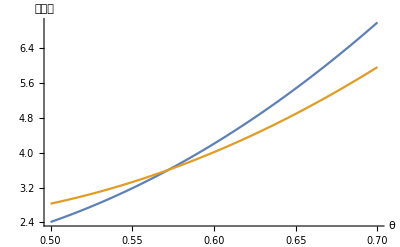

```mathematica
Plot[{mπr,rπr},{θ,0.5,0.7},AxesLabel->{θ,忠诚度}]
```

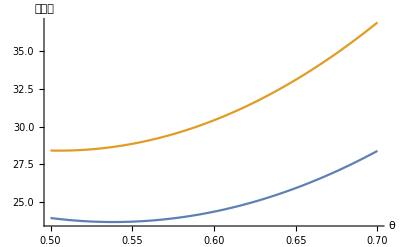

```mathematica
Plot[{mπm,rπm},{θ,0.5,0.7},AxesLabel->{θ,忠诚度}]
```

```mathematica
a=30
c=2
x=4
y=6
α=0.3
τ=0.5
μ=0.5
```